# Extended Hubbard Model

two-orbital Hubbard model with cosine higher bands

## Initialization cells

constant

```mathematica
a=1;
t1=1;
t1dash=0;
t2=0.1;
t2dash=0.4;
mu=0;
t3=10;
```

displacements

```mathematica
delta={a/2{1,√3},a/2{1,-√3},-a{1,0}};
fifthNN={3a{1,0},3/2 a{1,√3},3/2 a{-1,√3},3/2 a{-1,-√3},3/2 a{1,-√3},3a{-1,0}};
```

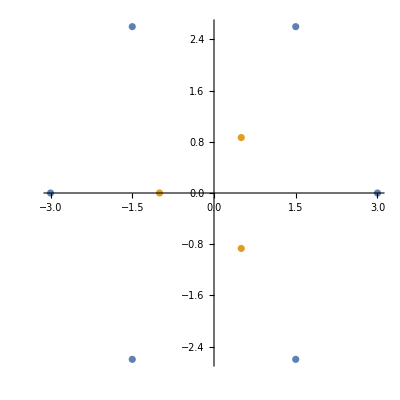

```mathematica
ListPlot[{fifthNN,delta}, AspectRatio->1]
```

k vector

```mathematica
k={kx,ky};
```

## SU(4) Hamiltonian

### Matrix form

```mathematica
M={{0,"A",0,0},{"Aconj",0,0,0},{0,0,0,"A"},{0,0,"Aconj",0}};
M//MatrixForm
Eigenvalues[M]
```

(0 | A | 0 | 0
Aconj | 0 | 0 | 0
0 | 0 | 0 | A
0 | 0 | Aconj | 0)

{-√A √Aconj,-√A √Aconj,√A √Aconj,√A √Aconj}

### Band structure

```mathematica
f=Assuming[{kx∈Reals,ky∈Reals},t1*Sum[Exp[ⅈ k.delta[[i]]],{i,1,3}]+t2*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
```

Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx]

```mathematica
g[kx_,ky_]=Abs[f]-0.5//ComplexExpand
```

-0.5+√((Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)])^2+(2 Cos[(√3 ky)/2] Sin[kx/2]-Sin[kx])^2)

```mathematica
Plot3D[g[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

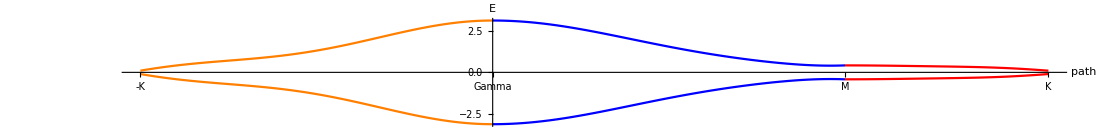

```mathematica
Show[{Plot[{g[kx,kx/(√3)],-g[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g[kx,0],-g[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g[2 π/3,(ky-2 π/3)],-g[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```

## SU(4) Hamiltonian with cosine bands

### Matrix form

```mathematica
M={{0,"A",0,0,0,0},{"Aconj",0,0,0,0,0},{0,0,0,"A",0,0},{0,0,"Aconj",0,0,0},{0,0,0,0,-"C","B"},{0,0,0,0,"Bconj","C"}};
M//MatrixForm
Eigenvalues[M]
```

(0 | A | 0 | 0 | 0 | 0
Aconj | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | A | 0 | 0
0 | 0 | Aconj | 0 | 0 | 0
0 | 0 | 0 | 0 | -C | B
0 | 0 | 0 | 0 | Bconj | C)

{-√A √Aconj,-√A √Aconj,√A √Aconj,√A √Aconj,-√(B Bconj+C^2),√(B Bconj+C^2)}

### Band structure

```mathematica
f=Assuming[{kx∈Reals,ky∈Reals},t1*Sum[Exp[ⅈ k.delta[[i]]],{i,1,3}]+t2*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
```

Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx]

```mathematica
f2=Assuming[{kx∈Reals,ky∈Reals},t3*Sum[Exp[ⅈ k.delta[[i]]],{i,1,3}]]//ComplexExpand//FullSimplify
f2conj=Conjugate[f2]//ComplexExpand//FullSimplify
```

10 (Cos[kx]+2 ⅇ^((ⅈ kx)/2) Cos[(√3 ky)/2]-ⅈ Sin[kx])

10 ⅇ^(ⅈ kx)+20 ⅇ^(-(ⅈ kx)/2) Cos[(√3 ky)/2]

```mathematica
g[kx_,ky_]=Abs[f]//ComplexExpand
```

√((Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)])^2+(2 Cos[(√3 ky)/2] Sin[kx/2]-Sin[kx])^2)

```mathematica
g2[kx_,ky_]=√(f2*f2conj+30^2)//ComplexExpand//FullSimplify
```

10 √2 ⅇ^(1/2 ⅈ Arg[6+2 Cos[(3 kx)/2] Cos[(√3 ky)/2]+Cos[√3 ky]]) ((6+2 Cos[(3 kx)/2] Cos[(√3 ky)/2]+Cos[√3 ky])^2)^(1/4)

```mathematica
Plot3D[g[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

```mathematica
Plot3D[g2[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

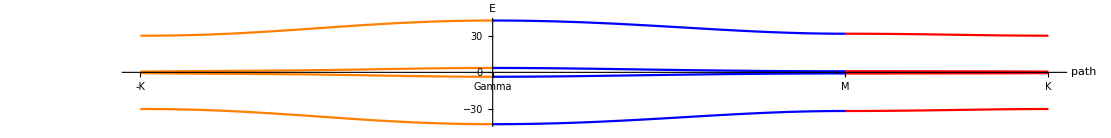

```mathematica
Show[{Plot[{g[kx,kx/(√3)],-g[kx,kx/(√3)],g2[kx,kx/(√3)],-g2[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g[kx,0],-g[kx,0],g2[kx,0],-g2[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g[2 π/3,(ky-2 π/3)],-g[2 π/3,(ky-2 π/3)],g2[2 π/3,(ky-2 π/3)],-g2[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```

## U(1) x SU(2) Hamiltonian

### Matrix form

```mathematica
M={{0,"A",0,"B"},{"Aconj",0,"F",0},{0,"Fconj",0,"A"},{"Bconj",0,"Aconj",0}};
M//MatrixForm
Eigenvalues[M]
```

(0 | A | 0 | B
Aconj | 0 | F | 0
0 | Fconj | 0 | A
Bconj | 0 | Aconj | 0)

{-(√(2 A Aconj+B Bconj+F Fconj-√(4 A Aconj B Bconj+B^2 Bconj^2+4 A^2 Bconj F+4 Aconj^2 B Fconj+4 A Aconj F Fconj-2 B Bconj F Fconj+F^2 Fconj^2)))/(√2),(√(2 A Aconj+B Bconj+F Fconj-√(4 A Aconj B Bconj+B^2 Bconj^2+4 A^2 Bconj F+4 Aconj^2 B Fconj+4 A Aconj F Fconj-2 B Bconj F Fconj+F^2 Fconj^2)))/(√2),-(√(2 A Aconj+B Bconj+F Fconj+√(4 A Aconj B Bconj+B^2 Bconj^2+4 A^2 Bconj F+4 Aconj^2 B Fconj+4 A Aconj F Fconj-2 B Bconj F Fconj+F^2 Fconj^2)))/(√2),(√(2 A Aconj+B Bconj+F Fconj+√(4 A Aconj B Bconj+B^2 Bconj^2+4 A^2 Bconj F+4 Aconj^2 B Fconj+4 A Aconj F Fconj-2 B Bconj F Fconj+F^2 Fconj^2)))/(√2)}

### Band structure

#### define symbols

```mathematica
A=Assuming[{kx∈Reals,ky∈Reals},t1*Sum[Exp[ⅈ k.delta[[i]]],{i,1,3}]+t2*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
A2 =A^2//ComplexExpand //Simplify
Aconj= Conjugate[A]//ComplexExpand //FullSimplify
Aconj2=Aconj^2//ComplexExpand //Simplify
AAconj=A*Aconj//ComplexExpand //FullSimplify
```

Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx]

Cos[kx]+Cos[kx]^2+0.04 Cos[3 kx]+0.4 Cos[kx] Cos[3 kx]+0.04 Cos[3 kx]^2+Cos[√3 ky]+0.04 Cos[3 √3 ky]+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+0.04 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+0.04 Cos[3/2 (kx+√3 ky)]^2-4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2+4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]-Sin[kx]^2+(0.+4. ⅈ) (0.5 Cos[1/2 (kx-2 √3 ky)] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx-√3 ky)] Sin[kx/2]+0.5 Cos[kx/2+√3 ky] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx+√3 ky)] Sin[kx/2]+Cos[kx] (Cos[(√3 ky)/2] Sin[kx/2]-0.5 Sin[kx])+Cos[3 kx] (0.2 Cos[(√3 ky)/2] Sin[kx/2]-0.1 Sin[kx])+0.5 Sin[kx]-0.5 Cos[1/2 (kx-√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx-√3 ky)] Sin[kx]-0.5 Cos[1/2 (kx+√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx+√3 ky)] Sin[kx])

Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+ⅈ (-2 Cos[(√3 ky)/2] Sin[kx/2]+Sin[kx])

Cos[kx]+Cos[kx]^2+0.04 Cos[3 kx]+0.4 Cos[kx] Cos[3 kx]+0.04 Cos[3 kx]^2+Cos[√3 ky]+0.04 Cos[3 √3 ky]+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+0.04 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+0.04 Cos[3/2 (kx+√3 ky)]^2-4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2+4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]-Sin[kx]^2-(0.+4. ⅈ) (0.5 Cos[1/2 (kx-2 √3 ky)] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx-√3 ky)] Sin[kx/2]+0.5 Cos[kx/2+√3 ky] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx+√3 ky)] Sin[kx/2]+Cos[kx] (Cos[(√3 ky)/2] Sin[kx/2]-0.5 Sin[kx])+Cos[3 kx] (0.2 Cos[(√3 ky)/2] Sin[kx/2]-0.1 Sin[kx])+0.5 Sin[kx]-0.5 Cos[1/2 (kx-√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx-√3 ky)] Sin[kx]-0.5 Cos[1/2 (kx+√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx+√3 ky)] Sin[kx])

3.06+0.2 Cos[2 kx]+0.04 Cos[3 kx]+0.2 Cos[4 kx]+0.02 Cos[6 kx]+2. Cos[√3 ky]+0.04 Cos[3 √3 ky]+0.2 Cos[1/2 (kx-3 √3 ky)]+0.2 Cos[1/2 (5 kx-3 √3 ky)]+0.2 Cos[kx-2 √3 ky]+0.2 Cos[kx-√3 ky]+0.04 Cos[3/2 (kx-√3 ky)]+0.2 Cos[2 (kx-√3 ky)]+0.02 Cos[3 (kx-√3 ky)]+0.2 Cos[2 kx-√3 ky]+2. Cos[1/2 (3 kx-√3 ky)]+0.04 Cos[3/2 (3 kx-√3 ky)]+0.2 Cos[1/2 (5 kx-√3 ky)]+0.2 Cos[1/2 (7 kx-√3 ky)]+0.2 Cos[kx+√3 ky]+0.04 Cos[3/2 (kx+√3 ky)]+0.2 Cos[2 (kx+√3 ky)]+0.02 Cos[3 (kx+√3 ky)]+0.2 Cos[2 kx+√3 ky]+2. Cos[1/2 (3 kx+√3 ky)]+0.04 Cos[3/2 (3 kx+√3 ky)]+0.2 Cos[1/2 (5 kx+√3 ky)]+0.2 Cos[1/2 (7 kx+√3 ky)]+0.2 Cos[kx+2 √3 ky]+0.2 Cos[1/2 (kx+3 √3 ky)]+0.2 Cos[1/2 (5 kx+3 √3 ky)]

```mathematica
B=Assuming[{kx∈Reals,ky∈Reals},t2dash*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
BBconj=B^2//ComplexExpand //FullSimplify
BBconj2 = BBconj^2//ComplexExpand //FullSimplify
```

0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]

0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)]

2.304+3.072 Cos[3 kx]+1.7408 Cos[6 kx]+0.6144 Cos[9 kx]+0.0512 Cos[12 kx]+(6.144 Cos[(3 kx)/2]+4.9152 Cos[(9 kx)/2]+1.6384 Cos[(15 kx)/2]+0.4096 Cos[(21 kx)/2]) Cos[(3 √3 ky)/2]+Cos[(3 kx)/2]^2 (4.096+1.6384 Cos[3 kx]+2.4576 Cos[6 kx]) Cos[3 √3 ky]+3.2768 Cos[(3 kx)/2]^3 Cos[3 kx] Cos[(9 √3 ky)/2]+0.8192 Cos[(3 kx)/2]^4 Cos[6 √3 ky]

```mathematica
F=Assuming[{kx∈Reals,ky∈Reals},-t2dash*Sum[Exp[ⅈ k.fifthNN[[i]]],{i,1,6}]]//ComplexExpand//FullSimplify
FFconj=F^2//ComplexExpand //FullSimplify
FFconj2 = FFconj^2//ComplexExpand //FullSimplify
```

-0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)]

0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)]

2.304+3.072 Cos[3 kx]+1.7408 Cos[6 kx]+0.6144 Cos[9 kx]+0.0512 Cos[12 kx]+(6.144 Cos[(3 kx)/2]+4.9152 Cos[(9 kx)/2]+1.6384 Cos[(15 kx)/2]+0.4096 Cos[(21 kx)/2]) Cos[(3 √3 ky)/2]+Cos[(3 kx)/2]^2 (4.096+1.6384 Cos[3 kx]+2.4576 Cos[6 kx]) Cos[3 √3 ky]+3.2768 Cos[(3 kx)/2]^3 Cos[3 kx] Cos[(9 √3 ky)/2]+0.8192 Cos[(3 kx)/2]^4 Cos[6 √3 ky]

```mathematica
mag=2*AAconj+BBconj+FFconj //ComplexExpand//FullSimplify
```

8.04+0.4 Cos[2 kx]+1.36 Cos[3 kx]+0.4 Cos[4 kx]+0.68 Cos[6 kx]+4. Cos[√3 ky]+1.36 Cos[3 √3 ky]+0.4 Cos[1/2 (kx-3 √3 ky)]+0.4 Cos[1/2 (5 kx-3 √3 ky)]+0.4 Cos[kx-2 √3 ky]+0.4 Cos[kx-√3 ky]+1.36 Cos[3/2 (kx-√3 ky)]+0.4 Cos[2 (kx-√3 ky)]+0.68 Cos[3 (kx-√3 ky)]+0.4 Cos[2 kx-√3 ky]+4. Cos[1/2 (3 kx-√3 ky)]+1.36 Cos[3/2 (3 kx-√3 ky)]+0.4 Cos[1/2 (5 kx-√3 ky)]+0.4 Cos[1/2 (7 kx-√3 ky)]+0.4 Cos[kx+√3 ky]+1.36 Cos[3/2 (kx+√3 ky)]+0.4 Cos[2 (kx+√3 ky)]+0.68 Cos[3 (kx+√3 ky)]+0.4 Cos[2 kx+√3 ky]+4. Cos[1/2 (3 kx+√3 ky)]+1.36 Cos[3/2 (3 kx+√3 ky)]+0.4 Cos[1/2 (5 kx+√3 ky)]+0.4 Cos[1/2 (7 kx+√3 ky)]+0.4 Cos[kx+2 √3 ky]+0.4 Cos[1/2 (kx+3 √3 ky)]+0.4 Cos[1/2 (5 kx+3 √3 ky)]

#### final function (negative root inside)

```mathematica
g2[kx_,ky_]=(√(mag-√(4 *AAconj*BBconj+BBconj2+4*A2*B*F+4*Aconj2*B*F+4*AAconj*FFconj-2*BBconj*FFconj+FFconj2)))/(√2)
```

1/(√2)(√(8.04+0.4 Cos[2 kx]+1.36 Cos[3 kx]+0.4 Cos[4 kx]+0.68 Cos[6 kx]+4. Cos[√3 ky]+1.36 Cos[3 √3 ky]+0.4 Cos[1/2 (kx-3 √3 ky)]+0.4 Cos[1/2 (5 kx-3 √3 ky)]+0.4 Cos[kx-2 √3 ky]+0.4 Cos[kx-√3 ky]+1.36 Cos[3/2 (kx-√3 ky)]+0.4 Cos[2 (kx-√3 ky)]+0.68 Cos[3 (kx-√3 ky)]+0.4 Cos[2 kx-√3 ky]+4. Cos[1/2 (3 kx-√3 ky)]+1.36 Cos[3/2 (3 kx-√3 ky)]+0.4 Cos[1/2 (5 kx-√3 ky)]+0.4 Cos[1/2 (7 kx-√3 ky)]+0.4 Cos[kx+√3 ky]+1.36 Cos[3/2 (kx+√3 ky)]+0.4 Cos[2 (kx+√3 ky)]+0.68 Cos[3 (kx+√3 ky)]+0.4 Cos[2 kx+√3 ky]+4. Cos[1/2 (3 kx+√3 ky)]+1.36 Cos[3/2 (3 kx+√3 ky)]+0.4 Cos[1/2 (5 kx+√3 ky)]+0.4 Cos[1/2 (7 kx+√3 ky)]+0.4 Cos[kx+2 √3 ky]+0.4 Cos[1/2 (kx+3 √3 ky)]+0.4 Cos[1/2 (5 kx+3 √3 ky)]-√(4.608+6.144 Cos[3 kx]+3.4816 Cos[6 kx]+1.2288 Cos[9 kx]+0.1024 Cos[12 kx]+2 (6.144 Cos[(3 kx)/2]+4.9152 Cos[(9 kx)/2]+1.6384 Cos[(15 kx)/2]+0.4096 Cos[(21 kx)/2]) Cos[(3 √3 ky)/2]+2 Cos[(3 kx)/2]^2 (4.096+1.6384 Cos[3 kx]+2.4576 Cos[6 kx]) Cos[3 √3 ky]+6.5536 Cos[(3 kx)/2]^3 Cos[3 kx] Cos[(9 √3 ky)/2]+1.6384 Cos[(3 kx)/2]^4 Cos[6 √3 ky]-2 (0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)])^2+8 (0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)]) (3.06+0.2 Cos[2 kx]+0.04 Cos[3 kx]+0.2 Cos[4 kx]+0.02 Cos[6 kx]+2. Cos[√3 ky]+0.04 Cos[3 √3 ky]+0.2 Cos[1/2 (kx-3 √3 ky)]+0.2 Cos[1/2 (5 kx-3 √3 ky)]+0.2 Cos[kx-2 √3 ky]+0.2 Cos[kx-√3 ky]+0.04 Cos[3/2 (kx-√3 ky)]+0.2 Cos[2 (kx-√3 ky)]+0.02 Cos[3 (kx-√3 ky)]+0.2 Cos[2 kx-√3 ky]+2. Cos[1/2 (3 kx-√3 ky)]+0.04 Cos[3/2 (3 kx-√3 ky)]+0.2 Cos[1/2 (5 kx-√3 ky)]+0.2 Cos[1/2 (7 kx-√3 ky)]+0.2 Cos[kx+√3 ky]+0.04 Cos[3/2 (kx+√3 ky)]+0.2 Cos[2 (kx+√3 ky)]+0.02 Cos[3 (kx+√3 ky)]+0.2 Cos[2 kx+√3 ky]+2. Cos[1/2 (3 kx+√3 ky)]+0.04 Cos[3/2 (3 kx+√3 ky)]+0.2 Cos[1/2 (5 kx+√3 ky)]+0.2 Cos[1/2 (7 kx+√3 ky)]+0.2 Cos[kx+2 √3 ky]+0.2 Cos[1/2 (kx+3 √3 ky)]+0.2 Cos[1/2 (5 kx+3 √3 ky)])+4 (-0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)]) (0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]) (Cos[kx]+Cos[kx]^2+0.04 Cos[3 kx]+0.4 Cos[kx] Cos[3 kx]+0.04 Cos[3 kx]^2+Cos[√3 ky]+0.04 Cos[3 √3 ky]+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+0.04 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+0.04 Cos[3/2 (kx+√3 ky)]^2-4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2+4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]-Sin[kx]^2-(0.+4. ⅈ) (0.5 Cos[1/2 (kx-2 √3 ky)] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx-√3 ky)] Sin[kx/2]+0.5 Cos[kx/2+√3 ky] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx+√3 ky)] Sin[kx/2]+Cos[kx] (Cos[(√3 ky)/2] Sin[kx/2]-0.5 Sin[kx])+Cos[3 kx] (0.2 Cos[(√3 ky)/2] Sin[kx/2]-0.1 Sin[kx])+0.5 Sin[kx]-0.5 Cos[1/2 (kx-√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx-√3 ky)] Sin[kx]-0.5 Cos[1/2 (kx+√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx+√3 ky)] Sin[kx]))+4 (-0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)]) (0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]) (Cos[kx]+Cos[kx]^2+0.04 Cos[3 kx]+0.4 Cos[kx] Cos[3 kx]+0.04 Cos[3 kx]^2+Cos[√3 ky]+0.04 Cos[3 √3 ky]+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+0.04 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+0.04 Cos[3/2 (kx+√3 ky)]^2-4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2+4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]-Sin[kx]^2+(0.+4. ⅈ) (0.5 Cos[1/2 (kx-2 √3 ky)] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx-√3 ky)] Sin[kx/2]+0.5 Cos[kx/2+√3 ky] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx+√3 ky)] Sin[kx/2]+Cos[kx] (Cos[(√3 ky)/2] Sin[kx/2]-0.5 Sin[kx])+Cos[3 kx] (0.2 Cos[(√3 ky)/2] Sin[kx/2]-0.1 Sin[kx])+0.5 Sin[kx]-0.5 Cos[1/2 (kx-√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx-√3 ky)] Sin[kx]-0.5 Cos[1/2 (kx+√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx+√3 ky)] Sin[kx])))))

```mathematica
Plot3D[g2[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

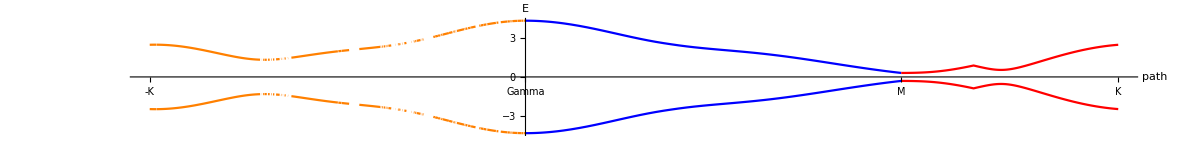

```mathematica
Show[{Plot[{g2[kx,kx/(√3)],-g2[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g2[kx,0],-g2[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g2[2 π/3,(ky-2 π/3)],-g2[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```

#### final function (positive root inside)

```mathematica
g3[kx_,ky_]=(√(mag+√(4 *AAconj*BBconj+BBconj2+4*A2*B*F+4*Aconj2*B*F+4*AAconj*FFconj-2*BBconj*FFconj+FFconj2)))/(√2)
```

1/(√2)(√(8.04+0.4 Cos[2 kx]+1.36 Cos[3 kx]+0.4 Cos[4 kx]+0.68 Cos[6 kx]+4. Cos[√3 ky]+1.36 Cos[3 √3 ky]+0.4 Cos[1/2 (kx-3 √3 ky)]+0.4 Cos[1/2 (5 kx-3 √3 ky)]+0.4 Cos[kx-2 √3 ky]+0.4 Cos[kx-√3 ky]+1.36 Cos[3/2 (kx-√3 ky)]+0.4 Cos[2 (kx-√3 ky)]+0.68 Cos[3 (kx-√3 ky)]+0.4 Cos[2 kx-√3 ky]+4. Cos[1/2 (3 kx-√3 ky)]+1.36 Cos[3/2 (3 kx-√3 ky)]+0.4 Cos[1/2 (5 kx-√3 ky)]+0.4 Cos[1/2 (7 kx-√3 ky)]+0.4 Cos[kx+√3 ky]+1.36 Cos[3/2 (kx+√3 ky)]+0.4 Cos[2 (kx+√3 ky)]+0.68 Cos[3 (kx+√3 ky)]+0.4 Cos[2 kx+√3 ky]+4. Cos[1/2 (3 kx+√3 ky)]+1.36 Cos[3/2 (3 kx+√3 ky)]+0.4 Cos[1/2 (5 kx+√3 ky)]+0.4 Cos[1/2 (7 kx+√3 ky)]+0.4 Cos[kx+2 √3 ky]+0.4 Cos[1/2 (kx+3 √3 ky)]+0.4 Cos[1/2 (5 kx+3 √3 ky)]+√(4.608+6.144 Cos[3 kx]+3.4816 Cos[6 kx]+1.2288 Cos[9 kx]+0.1024 Cos[12 kx]+2 (6.144 Cos[(3 kx)/2]+4.9152 Cos[(9 kx)/2]+1.6384 Cos[(15 kx)/2]+0.4096 Cos[(21 kx)/2]) Cos[(3 √3 ky)/2]+2 Cos[(3 kx)/2]^2 (4.096+1.6384 Cos[3 kx]+2.4576 Cos[6 kx]) Cos[3 √3 ky]+6.5536 Cos[(3 kx)/2]^3 Cos[3 kx] Cos[(9 √3 ky)/2]+1.6384 Cos[(3 kx)/2]^4 Cos[6 √3 ky]-2 (0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)])^2+8 (0.64+0.64 Cos[3 √3 ky]+0.32 Cos[3 (kx-√3 ky)]+Cos[3 kx] (0.64+0.64 Cos[3 kx]+1.28 Cos[3/2 (kx-√3 ky)]+1.28 Cos[3/2 (kx+√3 ky)])+0.32 Cos[3 (kx+√3 ky)]) (3.06+0.2 Cos[2 kx]+0.04 Cos[3 kx]+0.2 Cos[4 kx]+0.02 Cos[6 kx]+2. Cos[√3 ky]+0.04 Cos[3 √3 ky]+0.2 Cos[1/2 (kx-3 √3 ky)]+0.2 Cos[1/2 (5 kx-3 √3 ky)]+0.2 Cos[kx-2 √3 ky]+0.2 Cos[kx-√3 ky]+0.04 Cos[3/2 (kx-√3 ky)]+0.2 Cos[2 (kx-√3 ky)]+0.02 Cos[3 (kx-√3 ky)]+0.2 Cos[2 kx-√3 ky]+2. Cos[1/2 (3 kx-√3 ky)]+0.04 Cos[3/2 (3 kx-√3 ky)]+0.2 Cos[1/2 (5 kx-√3 ky)]+0.2 Cos[1/2 (7 kx-√3 ky)]+0.2 Cos[kx+√3 ky]+0.04 Cos[3/2 (kx+√3 ky)]+0.2 Cos[2 (kx+√3 ky)]+0.02 Cos[3 (kx+√3 ky)]+0.2 Cos[2 kx+√3 ky]+2. Cos[1/2 (3 kx+√3 ky)]+0.04 Cos[3/2 (3 kx+√3 ky)]+0.2 Cos[1/2 (5 kx+√3 ky)]+0.2 Cos[1/2 (7 kx+√3 ky)]+0.2 Cos[kx+2 √3 ky]+0.2 Cos[1/2 (kx+3 √3 ky)]+0.2 Cos[1/2 (5 kx+3 √3 ky)])+4 (-0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)]) (0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]) (Cos[kx]+Cos[kx]^2+0.04 Cos[3 kx]+0.4 Cos[kx] Cos[3 kx]+0.04 Cos[3 kx]^2+Cos[√3 ky]+0.04 Cos[3 √3 ky]+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+0.04 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+0.04 Cos[3/2 (kx+√3 ky)]^2-4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2+4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]-Sin[kx]^2-(0.+4. ⅈ) (0.5 Cos[1/2 (kx-2 √3 ky)] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx-√3 ky)] Sin[kx/2]+0.5 Cos[kx/2+√3 ky] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx+√3 ky)] Sin[kx/2]+Cos[kx] (Cos[(√3 ky)/2] Sin[kx/2]-0.5 Sin[kx])+Cos[3 kx] (0.2 Cos[(√3 ky)/2] Sin[kx/2]-0.1 Sin[kx])+0.5 Sin[kx]-0.5 Cos[1/2 (kx-√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx-√3 ky)] Sin[kx]-0.5 Cos[1/2 (kx+√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx+√3 ky)] Sin[kx]))+4 (-0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)]) (0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]) (Cos[kx]+Cos[kx]^2+0.04 Cos[3 kx]+0.4 Cos[kx] Cos[3 kx]+0.04 Cos[3 kx]^2+Cos[√3 ky]+0.04 Cos[3 √3 ky]+2 Cos[kx] Cos[1/2 (kx-√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx-√3 ky)]+Cos[1/2 (kx-√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx-√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx-√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx-√3 ky)]+0.04 Cos[3/2 (kx-√3 ky)]^2+2 Cos[kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3 kx] Cos[1/2 (kx+√3 ky)]+0.4 Cos[3/2 (kx-√3 ky)] Cos[1/2 (kx+√3 ky)]+Cos[1/2 (kx+√3 ky)]^2+0.4 Cos[kx] Cos[3/2 (kx+√3 ky)]+0.08 Cos[3 kx] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx-√3 ky)] Cos[3/2 (kx+√3 ky)]+0.4 Cos[1/2 (kx+√3 ky)] Cos[3/2 (kx+√3 ky)]+0.04 Cos[3/2 (kx+√3 ky)]^2-4 Cos[(√3 ky)/2]^2 Sin[kx/2]^2+4 Cos[(√3 ky)/2] Sin[kx/2] Sin[kx]-Sin[kx]^2+(0.+4. ⅈ) (0.5 Cos[1/2 (kx-2 √3 ky)] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx-√3 ky)] Sin[kx/2]+0.5 Cos[kx/2+√3 ky] Sin[kx/2]+0.2 Cos[(√3 ky)/2] Cos[3/2 (kx+√3 ky)] Sin[kx/2]+Cos[kx] (Cos[(√3 ky)/2] Sin[kx/2]-0.5 Sin[kx])+Cos[3 kx] (0.2 Cos[(√3 ky)/2] Sin[kx/2]-0.1 Sin[kx])+0.5 Sin[kx]-0.5 Cos[1/2 (kx-√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx-√3 ky)] Sin[kx]-0.5 Cos[1/2 (kx+√3 ky)] Sin[kx]-0.1 Cos[3/2 (kx+√3 ky)] Sin[kx])))))

```mathematica
Plot3D[g3[kx,ky],{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

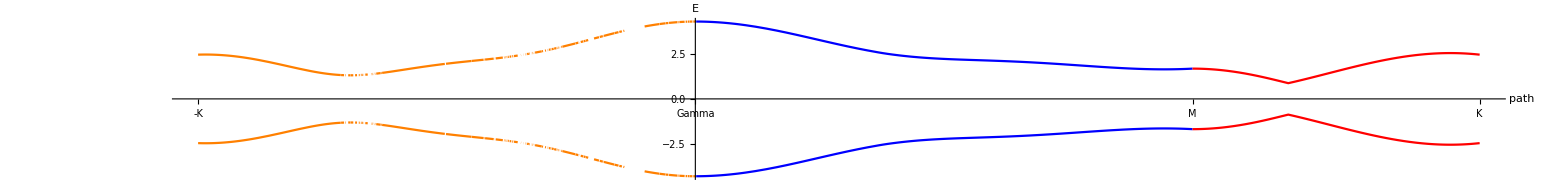

```mathematica
Show[{Plot[{g3[kx,kx/(√3)],-g3[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g3[kx,0],-g3[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g3[2 π/3,(ky-2 π/3)],-g3[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```

#### final function (combined)

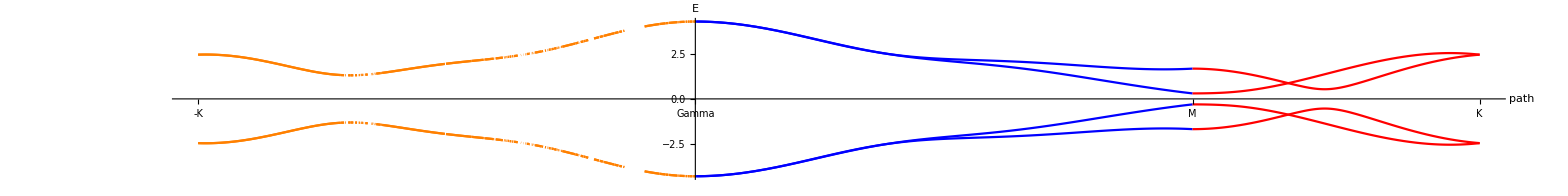

```mathematica
Show[{Plot[{g2[kx,kx/(√3)],-g2[kx,kx/(√3)],g3[kx,kx/(√3)],-g3[kx,kx/(√3)]},{kx,-(2π)/3,0},PlotStyle->Orange],Plot[{g2[kx,0],-g2[kx,0],g3[kx,0],-g3[kx,0]},{kx,0,(2π)/3},PlotStyle->Blue],Plot[{g2[2 π/3,(ky-2 π/3)],-g2[2 π/3,(ky-2 π/3)],g3[2 π/3,(ky-2 π/3)],-g3[2 π/3,(ky-2 π/3)]},{ky,(2π)/3,(2π)/3+(2π)/(3 √3)},PlotStyle->Red]},AxesOrigin->{0,0},PlotRange->{Automatic,Automatic}, AxesLabel->{"path","E"},Ticks->{{{-2 π/3,"-K"},{0,"Gamma"},{(2π)/3,"M"},{(2π)/3+(2π)/(3 √3),"K"}},Automatic},AspectRatio->1/8]
```

### Complete Hamiltonian Matrix

```mathematica
M={{0,A,0,B},{Aconj,0,F,0},{0,F,0,A},{B,0,Aconj,0}};
M//MatrixForm
first=Eigenvalues[M][[1]]//ComplexExpand//Simplify//Chop
```

(0 | Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx] | 0 | 0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)]
Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+ⅈ (-2 Cos[(√3 ky)/2] Sin[kx/2]+Sin[kx]) | 0 | -0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)] | 0
0 | -0.8 Cos[3 kx]-0.8 Cos[3/2 (kx-√3 ky)]-0.8 Cos[3/2 (kx+√3 ky)] | 0 | Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+2 ⅈ Cos[(√3 ky)/2] Sin[kx/2]-ⅈ Sin[kx]
0.8 Cos[3 kx]+0.8 Cos[3/2 (kx-√3 ky)]+0.8 Cos[3/2 (kx+√3 ky)] | 0 | Cos[kx]+0.2 Cos[3 kx]+Cos[1/2 (kx-√3 ky)]+0.2 Cos[3/2 (kx-√3 ky)]+Cos[1/2 (kx+√3 ky)]+0.2 Cos[3/2 (kx+√3 ky)]+ⅈ (-2 Cos[(√3 ky)/2] Sin[kx/2]+Sin[kx]) | 0)

ⅈ Im[Root[633.945+248.304 Cos[kx]+249.827 Cos[2 kx]+275.017 Cos[3 kx]+163.322 Cos[4 kx]+88.8581 Cos[5 kx]+76.3045 Cos[6 kx]+37.6471 Cos[7 kx]+14.1176 Cos[8 kx]+24. Cos[9 kx]+2.35294 Cos[10 kx]+2. Cos[12 kx]+581.315 Cos[√3 ky]+85.8131 Cos[2 √3 ky]+112.609 Cos[3 √3 ky]+5.53633 Cos[4 √3 ky]+12. Cos[6 √3 ky]+8. Cos[3 kx-6 √3 ky]+2. Cos[6 kx-6 √3 ky]+7.05882 Cos[kx-5 √3 ky]+7.05882 Cos[2 kx-5 √3 ky]+2.35294 Cos[4 kx-5 √3 ky]+2.35294 Cos[5 kx-5 √3 ky]+7.05882 Cos[kx/2-(9 √3 ky)/2]+32. Cos[(3 kx)/2-(9 √3 ky)/2]+7.05882 Cos[(5 kx)/2-(9 √3 ky)/2]+2.35294 Cos[(7 kx)/2-(9 √3 ky)/2]+24. Cos[(9 kx)/2-(9 √3 ky)/2]+2.35294 Cos[(11 kx)/2-(9 √3 ky)/2]+8. Cos[(15 kx)/2-(9 √3 ky)/2]+30.5882 Cos[kx-4 √3 ky]+18.8235 Cos[2 kx-4 √3 ky]+2.76817 Cos[3 kx-4 √3 ky]+14.1176 Cos[4 kx-4 √3 ky]+2.35294 Cos[5 kx-4 √3 ky]+61.1765 Cos[kx/2-(7 √3 ky)/2]+8.3045 Cos[(3 kx)/2-(7 √3 ky)/2]+37.6471 Cos[(5 kx)/2-(7 √3 ky)/2]+37.6471 Cos[(7 kx)/2-(7 √3 ky)/2]+2.76817 Cos[(9 kx)/2-(7 √3 ky)/2]+7.05882 Cos[(11 kx)/2-(7 √3 ky)/2]+7.05882 Cos[(13 kx)/2-(7 √3 ky)/2]+86.782 Cos[kx-3 √3 ky]+75.0173 Cos[2 kx-3 √3 ky]+76.3045 Cos[3 kx-3 √3 ky]+37.6471 Cos[4 kx-3 √3 ky]+18.8235 Cos[5 kx-3 √3 ky]+32. Cos[6 kx-3 √3 ky]+7.05882 Cos[7 kx-3 √3 ky]+12. Cos[9 kx-3 √3 ky]+126.228 Cos[kx/2-(5 √3 ky)/2]+13.8408 Cos[(3 kx)/2-(5 √3 ky)/2]+88.8581 Cos[(5 kx)/2-(5 √3 ky)/2]+75.0173 Cos[(7 kx)/2-(5 √3 ky)/2]+8.3045 Cos[(9 kx)/2-(5 √3 ky)/2]+30.5882 Cos[(11 kx)/2-(5 √3 ky)/2]+7.05882 Cos[(13 kx)/2-(5 √3 ky)/2]+188.927 Cos[kx-2 √3 ky]+163.322 Cos[2 kx-2 √3 ky]+13.8408 Cos[3 kx-2 √3 ky]+86.782 Cos[4 kx-2 √3 ky]+61.1765 Cos[5 kx-2 √3 ky]+5.53633 Cos[6 kx-2 √3 ky]+7.05882 Cos[7 kx-2 √3 ky]+7.05882 Cos[8 kx-2 √3 ky]+202.768 Cos[kx/2-(3 √3 ky)/2]+275.017 Cos[(3 kx)/2-(3 √3 ky)/2]+188.927 Cos[(5 kx)/2-(3 √3 ky)/2]+126.228 Cos[(7 kx)/2-(3 √3 ky)/2]+112.609 Cos[(9 kx)/2-(3 √3 ky)/2]+61.1765 Cos[(11 kx)/2-(3 √3 ky)/2]+30.5882 Cos[(13 kx)/2-(3 √3 ky)/2]+32. Cos[(15 kx)/2-(3 √3 ky)/2]+7.05882 Cos[(17 kx)/2-(3 √3 ky)/2]+8. Cos[(21 kx)/2-(3 √3 ky)/2]+249.827 Cos[kx-√3 ky]+202.768 Cos[2 kx-√3 ky]+85.8131 Cos[3 kx-√3 ky]+126.228 Cos[4 kx-√3 ky]+86.782 Cos[5 kx-√3 ky]+8.3045 Cos[6 kx-√3 ky]+18.8235 Cos[7 kx-√3 ky]+7.05882 Cos[8 kx-√3 ky]+248.304 Cos[kx/2-(√3 ky)/2]+581.315 Cos[(3 kx)/2-(√3 ky)/2]+202.768 Cos[(5 kx)/2-(√3 ky)/2]+188.927 Cos[(7 kx)/2-(√3 ky)/2]+13.8408 Cos[(9 kx)/2-(√3 ky)/2]+75.0173 Cos[(11 kx)/2-(√3 ky)/2]+37.6471 Cos[(13 kx)/2-(√3 ky)/2]+2.76817 Cos[(15 kx)/2-(√3 ky)/2]+2.35294 Cos[(17 kx)/2-(√3 ky)/2]+2.35294 Cos[(19 kx)/2-(√3 ky)/2]+248.304 Cos[kx/2+(√3 ky)/2]+581.315 Cos[(3 kx)/2+(√3 ky)/2]+202.768 Cos[(5 kx)/2+(√3 ky)/2]+188.927 Cos[(7 kx)/2+(√3 ky)/2]+13.8408 Cos[(9 kx)/2+(√3 ky)/2]+75.0173 Cos[(11 kx)/2+(√3 ky)/2]+37.6471 Cos[(13 kx)/2+(√3 ky)/2]+2.76817 Cos[(15 kx)/2+(√3 ky)/2]+2.35294 Cos[(17 kx)/2+(√3 ky)/2]+2.35294 Cos[(19 kx)/2+(√3 ky)/2]+249.827 Cos[kx+√3 ky]+202.768 Cos[2 kx+√3 ky]+85.8131 Cos[3 kx+√3 ky]+126.228 Cos[4 kx+√3 ky]+86.782 Cos[5 kx+√3 ky]+8.3045 Cos[6 kx+√3 ky]+18.8235 Cos[7 kx+√3 ky]+7.05882 Cos[8 kx+√3 ky]+202.768 Cos[kx/2+(3 √3 ky)/2]+275.017 Cos[(3 kx)/2+(3 √3 ky)/2]+188.927 Cos[(5 kx)/2+(3 √3 ky)/2]+126.228 Cos[(7 kx)/2+(3 √3 ky)/2]+112.609 Cos[(9 kx)/2+(3 √3 ky)/2]+61.1765 Cos[(11 kx)/2+(3 √3 ky)/2]+30.5882 Cos[(13 kx)/2+(3 √3 ky)/2]+32. Cos[(15 kx)/2+(3 √3 ky)/2]+7.05882 Cos[(17 kx)/2+(3 √3 ky)/2]+8. Cos[(21 kx)/2+(3 √3 ky)/2]+188.927 Cos[kx+2 √3 ky]+163.322 Cos[2 kx+2 √3 ky]+13.8408 Cos[3 kx+2 √3 ky]+86.782 Cos[4 kx+2 √3 ky]+61.1765 Cos[5 kx+2 √3 ky]+5.53633 Cos[6 kx+2 √3 ky]+7.05882 Cos[7 kx+2 √3 ky]+7.05882 Cos[8 kx+2 √3 ky]+126.228 Cos[kx/2+(5 √3 ky)/2]+13.8408 Cos[(3 kx)/2+(5 √3 ky)/2]+88.8581 Cos[(5 kx)/2+(5 √3 ky)/2]+75.0173 Cos[(7 kx)/2+(5 √3 ky)/2]+8.3045 Cos[(9 kx)/2+(5 √3 ky)/2]+30.5882 Cos[(11 kx)/2+(5 √3 ky)/2]+7.05882 Cos[(13 kx)/2+(5 √3 ky)/2]+86.782 Cos[kx+3 √3 ky]+75.0173 Cos[2 kx+3 √3 ky]+76.3045 Cos[3 kx+3 √3 ky]+37.6471 Cos[4 kx+3 √3 ky]+18.8235 Cos[5 kx+3 √3 ky]+32. Cos[6 kx+3 √3 ky]+7.05882 Cos[7 kx+3 √3 ky]+12. Cos[9 kx+3 √3 ky]+61.1765 Cos[kx/2+(7 √3 ky)/2]+8.3045 Cos[(3 kx)/2+(7 √3 ky)/2]+37.6471 Cos[(5 kx)/2+(7 √3 ky)/2]+37.6471 Cos[(7 kx)/2+(7 √3 ky)/2]+2.76817 Cos[(9 kx)/2+(7 √3 ky)/2]+7.05882 Cos[(11 kx)/2+(7 √3 ky)/2]+7.05882 Cos[(13 kx)/2+(7 √3 ky)/2]+30.5882 Cos[kx+4 √3 ky]+18.8235 Cos[2 kx+4 √3 ky]+2.76817 Cos[3 kx+4 √3 ky]+14.1176 Cos[4 kx+4 √3 ky]+2.35294 Cos[5 kx+4 √3 ky]+7.05882 Cos[kx/2+(9 √3 ky)/2]+32. Cos[(3 kx)/2+(9 √3 ky)/2]+7.05882 Cos[(5 kx)/2+(9 √3 ky)/2]+2.35294 Cos[(7 kx)/2+(9 √3 ky)/2]+24. Cos[(9 kx)/2+(9 √3 ky)/2]+2.35294 Cos[(11 kx)/2+(9 √3 ky)/2]+8. Cos[(15 kx)/2+(9 √3 ky)/2]+7.05882 Cos[kx+5 √3 ky]+7.05882 Cos[2 kx+5 √3 ky]+2.35294 Cos[4 kx+5 √3 ky]+2.35294 Cos[5 kx+5 √3 ky]+8. Cos[3 kx+6 √3 ky]+2. Cos[6 kx+6 √3 ky]+(-278.201-13.8408 Cos[2 kx]-47.0588 Cos[3 kx]-13.8408 Cos[4 kx]-23.5294 Cos[6 kx]-138.408 Cos[√3 ky]-47.0588 Cos[3 √3 ky]-23.5294 Cos[3 kx-3 √3 ky]-13.8408 Cos[kx-2 √3 ky]-13.8408 Cos[2 kx-2 √3 ky]-13.8408 Cos[kx/2-(3 √3 ky)/2]-47.0588 Cos[(3 kx)/2-(3 √3 ky)/2]-13.8408 Cos[(5 kx)/2-(3 √3 ky)/2]-47.0588 Cos[(9 kx)/2-(3 √3 ky)/2]-13.8408 Cos[kx-√3 ky]-13.8408 Cos[2 kx-√3 ky]-138.408 Cos[(3 kx)/2-(√3 ky)/2]-13.8408 Cos[(5 kx)/2-(√3 ky)/2]-13.8408 Cos[(7 kx)/2-(√3 ky)/2]-138.408 Cos[(3 kx)/2+(√3 ky)/2]-13.8408 Cos[(5 kx)/2+(√3 ky)/2]-13.8408 Cos[(7 kx)/2+(√3 ky)/2]-13.8408 Cos[kx+√3 ky]-13.8408 Cos[2 kx+√3 ky]-13.8408 Cos[kx/2+(3 √3 ky)/2]-47.0588 Cos[(3 kx)/2+(3 √3 ky)/2]-13.8408 Cos[(5 kx)/2+(3 √3 ky)/2]-47.0588 Cos[(9 kx)/2+(3 √3 ky)/2]-13.8408 Cos[kx+2 √3 ky]-13.8408 Cos[2 kx+2 √3 ky]-23.5294 Cos[3 kx+3 √3 ky]) #1^2+34.6021 #1^4&,1]]+Re[Root[633.945+248.304 Cos[kx]+249.827 Cos[2 kx]+275.017 Cos[3 kx]+163.322 Cos[4 kx]+88.8581 Cos[5 kx]+76.3045 Cos[6 kx]+37.6471 Cos[7 kx]+14.1176 Cos[8 kx]+24. Cos[9 kx]+2.35294 Cos[10 kx]+2. Cos[12 kx]+581.315 Cos[√3 ky]+85.8131 Cos[2 √3 ky]+112.609 Cos[3 √3 ky]+5.53633 Cos[4 √3 ky]+12. Cos[6 √3 ky]+8. Cos[3 kx-6 √3 ky]+2. Cos[6 kx-6 √3 ky]+7.05882 Cos[kx-5 √3 ky]+7.05882 Cos[2 kx-5 √3 ky]+2.35294 Cos[4 kx-5 √3 ky]+2.35294 Cos[5 kx-5 √3 ky]+7.05882 Cos[kx/2-(9 √3 ky)/2]+32. Cos[(3 kx)/2-(9 √3 ky)/2]+7.05882 Cos[(5 kx)/2-(9 √3 ky)/2]+2.35294 Cos[(7 kx)/2-(9 √3 ky)/2]+24. Cos[(9 kx)/2-(9 √3 ky)/2]+2.35294 Cos[(11 kx)/2-(9 √3 ky)/2]+8. Cos[(15 kx)/2-(9 √3 ky)/2]+30.5882 Cos[kx-4 √3 ky]+18.8235 Cos[2 kx-4 √3 ky]+2.76817 Cos[3 kx-4 √3 ky]+14.1176 Cos[4 kx-4 √3 ky]+2.35294 Cos[5 kx-4 √3 ky]+61.1765 Cos[kx/2-(7 √3 ky)/2]+8.3045 Cos[(3 kx)/2-(7 √3 ky)/2]+37.6471 Cos[(5 kx)/2-(7 √3 ky)/2]+37.6471 Cos[(7 kx)/2-(7 √3 ky)/2]+2.76817 Cos[(9 kx)/2-(7 √3 ky)/2]+7.05882 Cos[(11 kx)/2-(7 √3 ky)/2]+7.05882 Cos[(13 kx)/2-(7 √3 ky)/2]+86.782 Cos[kx-3 √3 ky]+75.0173 Cos[2 kx-3 √3 ky]+76.3045 Cos[3 kx-3 √3 ky]+37.6471 Cos[4 kx-3 √3 ky]+18.8235 Cos[5 kx-3 √3 ky]+32. Cos[6 kx-3 √3 ky]+7.05882 Cos[7 kx-3 √3 ky]+12. Cos[9 kx-3 √3 ky]+126.228 Cos[kx/2-(5 √3 ky)/2]+13.8408 Cos[(3 kx)/2-(5 √3 ky)/2]+88.8581 Cos[(5 kx)/2-(5 √3 ky)/2]+75.0173 Cos[(7 kx)/2-(5 √3 ky)/2]+8.3045 Cos[(9 kx)/2-(5 √3 ky)/2]+30.5882 Cos[(11 kx)/2-(5 √3 ky)/2]+7.05882 Cos[(13 kx)/2-(5 √3 ky)/2]+188.927 Cos[kx-2 √3 ky]+163.322 Cos[2 kx-2 √3 ky]+13.8408 Cos[3 kx-2 √3 ky]+86.782 Cos[4 kx-2 √3 ky]+61.1765 Cos[5 kx-2 √3 ky]+5.53633 Cos[6 kx-2 √3 ky]+7.05882 Cos[7 kx-2 √3 ky]+7.05882 Cos[8 kx-2 √3 ky]+202.768 Cos[kx/2-(3 √3 ky)/2]+275.017 Cos[(3 kx)/2-(3 √3 ky)/2]+188.927 Cos[(5 kx)/2-(3 √3 ky)/2]+126.228 Cos[(7 kx)/2-(3 √3 ky)/2]+112.609 Cos[(9 kx)/2-(3 √3 ky)/2]+61.1765 Cos[(11 kx)/2-(3 √3 ky)/2]+30.5882 Cos[(13 kx)/2-(3 √3 ky)/2]+32. Cos[(15 kx)/2-(3 √3 ky)/2]+7.05882 Cos[(17 kx)/2-(3 √3 ky)/2]+8. Cos[(21 kx)/2-(3 √3 ky)/2]+249.827 Cos[kx-√3 ky]+202.768 Cos[2 kx-√3 ky]+85.8131 Cos[3 kx-√3 ky]+126.228 Cos[4 kx-√3 ky]+86.782 Cos[5 kx-√3 ky]+8.3045 Cos[6 kx-√3 ky]+18.8235 Cos[7 kx-√3 ky]+7.05882 Cos[8 kx-√3 ky]+248.304 Cos[kx/2-(√3 ky)/2]+581.315 Cos[(3 kx)/2-(√3 ky)/2]+202.768 Cos[(5 kx)/2-(√3 ky)/2]+188.927 Cos[(7 kx)/2-(√3 ky)/2]+13.8408 Cos[(9 kx)/2-(√3 ky)/2]+75.0173 Cos[(11 kx)/2-(√3 ky)/2]+37.6471 Cos[(13 kx)/2-(√3 ky)/2]+2.76817 Cos[(15 kx)/2-(√3 ky)/2]+2.35294 Cos[(17 kx)/2-(√3 ky)/2]+2.35294 Cos[(19 kx)/2-(√3 ky)/2]+248.304 Cos[kx/2+(√3 ky)/2]+581.315 Cos[(3 kx)/2+(√3 ky)/2]+202.768 Cos[(5 kx)/2+(√3 ky)/2]+188.927 Cos[(7 kx)/2+(√3 ky)/2]+13.8408 Cos[(9 kx)/2+(√3 ky)/2]+75.0173 Cos[(11 kx)/2+(√3 ky)/2]+37.6471 Cos[(13 kx)/2+(√3 ky)/2]+2.76817 Cos[(15 kx)/2+(√3 ky)/2]+2.35294 Cos[(17 kx)/2+(√3 ky)/2]+2.35294 Cos[(19 kx)/2+(√3 ky)/2]+249.827 Cos[kx+√3 ky]+202.768 Cos[2 kx+√3 ky]+85.8131 Cos[3 kx+√3 ky]+126.228 Cos[4 kx+√3 ky]+86.782 Cos[5 kx+√3 ky]+8.3045 Cos[6 kx+√3 ky]+18.8235 Cos[7 kx+√3 ky]+7.05882 Cos[8 kx+√3 ky]+202.768 Cos[kx/2+(3 √3 ky)/2]+275.017 Cos[(3 kx)/2+(3 √3 ky)/2]+188.927 Cos[(5 kx)/2+(3 √3 ky)/2]+126.228 Cos[(7 kx)/2+(3 √3 ky)/2]+112.609 Cos[(9 kx)/2+(3 √3 ky)/2]+61.1765 Cos[(11 kx)/2+(3 √3 ky)/2]+30.5882 Cos[(13 kx)/2+(3 √3 ky)/2]+32. Cos[(15 kx)/2+(3 √3 ky)/2]+7.05882 Cos[(17 kx)/2+(3 √3 ky)/2]+8. Cos[(21 kx)/2+(3 √3 ky)/2]+188.927 Cos[kx+2 √3 ky]+163.322 Cos[2 kx+2 √3 ky]+13.8408 Cos[3 kx+2 √3 ky]+86.782 Cos[4 kx+2 √3 ky]+61.1765 Cos[5 kx+2 √3 ky]+5.53633 Cos[6 kx+2 √3 ky]+7.05882 Cos[7 kx+2 √3 ky]+7.05882 Cos[8 kx+2 √3 ky]+126.228 Cos[kx/2+(5 √3 ky)/2]+13.8408 Cos[(3 kx)/2+(5 √3 ky)/2]+88.8581 Cos[(5 kx)/2+(5 √3 ky)/2]+75.0173 Cos[(7 kx)/2+(5 √3 ky)/2]+8.3045 Cos[(9 kx)/2+(5 √3 ky)/2]+30.5882 Cos[(11 kx)/2+(5 √3 ky)/2]+7.05882 Cos[(13 kx)/2+(5 √3 ky)/2]+86.782 Cos[kx+3 √3 ky]+75.0173 Cos[2 kx+3 √3 ky]+76.3045 Cos[3 kx+3 √3 ky]+37.6471 Cos[4 kx+3 √3 ky]+18.8235 Cos[5 kx+3 √3 ky]+32. Cos[6 kx+3 √3 ky]+7.05882 Cos[7 kx+3 √3 ky]+12. Cos[9 kx+3 √3 ky]+61.1765 Cos[kx/2+(7 √3 ky)/2]+8.3045 Cos[(3 kx)/2+(7 √3 ky)/2]+37.6471 Cos[(5 kx)/2+(7 √3 ky)/2]+37.6471 Cos[(7 kx)/2+(7 √3 ky)/2]+2.76817 Cos[(9 kx)/2+(7 √3 ky)/2]+7.05882 Cos[(11 kx)/2+(7 √3 ky)/2]+7.05882 Cos[(13 kx)/2+(7 √3 ky)/2]+30.5882 Cos[kx+4 √3 ky]+18.8235 Cos[2 kx+4 √3 ky]+2.76817 Cos[3 kx+4 √3 ky]+14.1176 Cos[4 kx+4 √3 ky]+2.35294 Cos[5 kx+4 √3 ky]+7.05882 Cos[kx/2+(9 √3 ky)/2]+32. Cos[(3 kx)/2+(9 √3 ky)/2]+7.05882 Cos[(5 kx)/2+(9 √3 ky)/2]+2.35294 Cos[(7 kx)/2+(9 √3 ky)/2]+24. Cos[(9 kx)/2+(9 √3 ky)/2]+2.35294 Cos[(11 kx)/2+(9 √3 ky)/2]+8. Cos[(15 kx)/2+(9 √3 ky)/2]+7.05882 Cos[kx+5 √3 ky]+7.05882 Cos[2 kx+5 √3 ky]+2.35294 Cos[4 kx+5 √3 ky]+2.35294 Cos[5 kx+5 √3 ky]+8. Cos[3 kx+6 √3 ky]+2. Cos[6 kx+6 √3 ky]+(-278.201-13.8408 Cos[2 kx]-47.0588 Cos[3 kx]-13.8408 Cos[4 kx]-23.5294 Cos[6 kx]-138.408 Cos[√3 ky]-47.0588 Cos[3 √3 ky]-23.5294 Cos[3 kx-3 √3 ky]-13.8408 Cos[kx-2 √3 ky]-13.8408 Cos[2 kx-2 √3 ky]-13.8408 Cos[kx/2-(3 √3 ky)/2]-47.0588 Cos[(3 kx)/2-(3 √3 ky)/2]-13.8408 Cos[(5 kx)/2-(3 √3 ky)/2]-47.0588 Cos[(9 kx)/2-(3 √3 ky)/2]-13.8408 Cos[kx-√3 ky]-13.8408 Cos[2 kx-√3 ky]-138.408 Cos[(3 kx)/2-(√3 ky)/2]-13.8408 Cos[(5 kx)/2-(√3 ky)/2]-13.8408 Cos[(7 kx)/2-(√3 ky)/2]-138.408 Cos[(3 kx)/2+(√3 ky)/2]-13.8408 Cos[(5 kx)/2+(√3 ky)/2]-13.8408 Cos[(7 kx)/2+(√3 ky)/2]-13.8408 Cos[kx+√3 ky]-13.8408 Cos[2 kx+√3 ky]-13.8408 Cos[kx/2+(3 √3 ky)/2]-47.0588 Cos[(3 kx)/2+(3 √3 ky)/2]-13.8408 Cos[(5 kx)/2+(3 √3 ky)/2]-47.0588 Cos[(9 kx)/2+(3 √3 ky)/2]-13.8408 Cos[kx+2 √3 ky]-13.8408 Cos[2 kx+2 √3 ky]-23.5294 Cos[3 kx+3 √3 ky]) #1^2+34.6021 #1^4&,1]]

```mathematica
Plot3D[first,{kx,-π,π},{ky,-π,π},BoxRatios->{1,1,1},AxesLabel->{"kx","ky","E"}]
```

-Graphics3D-

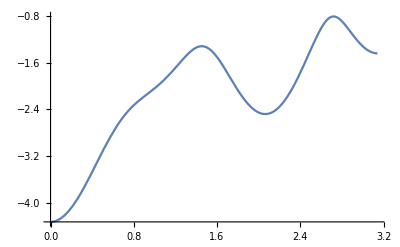

```mathematica
Plot[first/.ky->kx/√3,{kx,0,Pi}]
```